```mathematica
MakeBoxes[Σd,StandardForm]:=SubscriptBox["Σ","d"];MakeExpression[SubscriptBox["Σ","d"],StandardForm]:=MakeExpression["Σd",StandardForm];
MakeBoxes[Σod,StandardForm]:=SubscriptBox["Σ","od"];MakeExpression[SubscriptBox["Σ","od"],StandardForm]:=MakeExpression["Σod",StandardForm];
MakeBoxes[Σtd,StandardForm]:=SubscriptBox["Σ","td"];MakeExpression[SubscriptBox["Σ","td"],StandardForm]:=MakeExpression["Σtd",StandardForm];
MakeBoxes[Σtod,StandardForm]:=SubscriptBox["Σ","tod"];MakeExpression[SubscriptBox["Σ","tod"],StandardForm]:=MakeExpression["Σtod",StandardForm];
MakeBoxes[Φd,StandardForm]:=SubscriptBox["Φ","d"];MakeExpression[SubscriptBox["Φ","d"],StandardForm]:=MakeExpression["Φd",StandardForm];
MakeBoxes[Φod,StandardForm]:=SubscriptBox["Φ","od"];MakeExpression[SubscriptBox["Φ","od"],StandardForm]:=MakeExpression["Φod",StandardForm];
MakeBoxes[Φbd,StandardForm]:=SubscriptBox["Φ","bd"];MakeExpression[SubscriptBox["Φ","bd"],StandardForm]:=MakeExpression["Φbd",StandardForm];
MakeBoxes[Φbod,StandardForm]:=SubscriptBox["Φ","bod"];MakeExpression[SubscriptBox["Φ","bod"],StandardForm]:=MakeExpression["Φbod",StandardForm];

MakeBoxes[Σd,TraditionalForm]:=SubscriptBox["Σ","d"];MakeExpression[SubscriptBox["Σ","d"],TraditionalForm]:=MakeExpression["Σd",TraditionalForm];
MakeBoxes[Σod,TraditionalForm]:=SubscriptBox["Σ","od"];MakeExpression[SubscriptBox["Σ","od"],TraditionalForm]:=MakeExpression["Σod",TraditionalForm];
MakeBoxes[Σtd,TraditionalForm]:=SubscriptBox["Σ","td"];MakeExpression[SubscriptBox["Σ","td"],TraditionalForm]:=MakeExpression["Σtd",TraditionalForm];
MakeBoxes[Σtod,TraditionalForm]:=SubscriptBox["Σ","tod"];MakeExpression[SubscriptBox["Σ","tod"],TraditionalForm]:=MakeExpression["Σtod",TraditionalForm];
MakeBoxes[Φd,TraditionalForm]:=SubscriptBox["Φ","d"];MakeExpression[SubscriptBox["Φ","d"],TraditionalForm]:=MakeExpression["Φd",TraditionalForm];
MakeBoxes[Φod,TraditionalForm]:=SubscriptBox["Φ","od"];MakeExpression[SubscriptBox["Φ","od"],TraditionalForm]:=MakeExpression["Φod",TraditionalForm];
MakeBoxes[Φbd,TraditionalForm]:=SubscriptBox["Φ","bd"];MakeExpression[SubscriptBox["Φ","bd"],TraditionalForm]:=MakeExpression["Φbd",TraditionalForm];
MakeBoxes[Φbod,TraditionalForm]:=SubscriptBox["Φ","bod"];MakeExpression[SubscriptBox["Φ","bod"],TraditionalForm]:=MakeExpression["Φbod",TraditionalForm];
```

```mathematica
a = (I ω - Σd);
b = (-Φd );
c = (I ω - Σtd);
(*d = (-λ - Σod);*)
(*d = (-λ - Σod Exp[I θ]);*)
d = ( - Σod );
e = (-Φod);
(*f = (λ Exp[-I θ] - Σtod);*)
(*f = (λ- Σtod Exp[-I θ]);*)
f = (- Σtod);
g = -(Φbd);
h = -(Φbod);
(*A = {{a,b Exp[I θ]},{g Exp[-I θ],c}};
B = {{d Exp[I θ],e},{h,f Exp[-I θ]}};
L = {{d Exp[-I θ],e},{h,f Exp[I θ]}};
M = {{a,b Exp[-I θ]},{g Exp[I θ],c}};*)
(*A = {{a,b },{g ,c}};
B = {{d ,e},{h,f }};
L = {{d ,e},{h,f }};
M = {{a,b },{g ,c}};*)
(*A = {{a,b },{g ,c}};
B = {{-λ Exp[-I θ]+ d Exp[-I θ] ,e Exp[I θ]},{h Exp[-I θ],λ Exp[I θ]+ f Exp[I θ] }};
L = {{-λ Exp[I θ]+ d Exp[I θ],e Exp[I θ]},{h Exp[-I θ],λ Exp[-I θ] + f Exp[-I θ] }};
M = {{a,b Exp[2 I θ] },{g Exp[- 2I θ],c}};*)
A = {{a,b },{g ,c}};
B = {{-λ + d Exp[-I θ] ,e Exp[I θ]},{h Exp[-I θ],λ + f Exp[I θ] }};
L = {{-λ + d Exp[I θ],e Exp[I θ]},{h Exp[-I θ],λ  + f Exp[-I θ] }};
M = {{a,b Exp[2 I θ] },{g Exp[- 2I θ],c}};
(*A = {{a,b },{g ,c}};
B = {{-λ Exp[-I θ]+d ,e},{h,λ Exp[I θ]+f }};
L = {{-λ Exp[I θ]+ d  ,e},{h,λ Exp[-I θ]+ f}};
M = {{a,b },{g ,c}};*)
(*A = {{a,b },{g ,c}};
B = {{-λ + d  ,e },{h ,λ + f  }};
L = {{-λ + d ,e },{h ,λ  + f  }};
M = {{a,b Exp[2 I θ] },{g Exp[- 2I θ],c}};*)
Ginv = ArrayFlatten[{{A,B},{L,M}}];
Ginv//MatrixForm
asslist = {Element[ω,Reals],Element[λ,Reals],λ>0,Element[θ,Reals]};
redoneside  = {λ->0, Φod->0,Σtod->0,Σod->0, Φbod->0};
strreprule = {"(0,1)"->"1j", "Σd"-> "SigmaDomega","Σod"-> "SigmaODomega", "Φd"-> "PhiDomega","Φod"-> "PhiODomega","λ"->"lamb","ω"->"omega", "Im"->"np.imag" ,"(0,-1)"->"-1j","Cos"->"np.cos","Abs"->"np.abs", "θ"-> "theta", "Re"->"np.real"};
repst = {Σtd-> -Conjugate@Σd, Σtod-> -Conjugate@Σod, Φbd->Conjugate@Φd, Φbod->Conjugate@Φod};
redMET = {Φd -> 0, Φod -> 0, Φbd -> 0, Φbod -> 0};
spsymmreprule = {Conjugate[Σod]->Σod, Conjugate[Σd]-> -Σd};
detGinv = FullSimplify[Det[Ginv],Assumptions->asslist];
detGinv
```

(-Σ_d+ⅈ ω | -Φ_d | -λ-ⅇ^(-ⅈ θ) Σ_od | -ⅇ^(ⅈ θ) Φ_od
-Φ_bd | -Σ_td+ⅈ ω | -ⅇ^(-ⅈ θ) Φ_bod | λ-ⅇ^(ⅈ θ) Σ_tod
-λ-ⅇ^(ⅈ θ) Σ_od | -ⅇ^(ⅈ θ) Φ_od | -Σ_d+ⅈ ω | -ⅇ^(2 ⅈ θ) Φ_d
-ⅇ^(-ⅈ θ) Φ_bod | λ-ⅇ^(-ⅈ θ) Σ_tod | -ⅇ^(-2 ⅈ θ) Φ_bd | -Σ_td+ⅈ ω)

λ^4+(-((Φ_bd-Φ_bod) (Φ_d-Φ_od))+(Σ_d-Σ_od-ⅈ ω) (Σ_td-Σ_tod-ⅈ ω)) (-((Φ_bd+Φ_bod) (Φ_d+Φ_od))+(Σ_d+Σ_od-ⅈ ω) (Σ_td+Σ_tod-ⅈ ω))+λ^2 (-Σ_d^2-Σ_td^2+(Σ_od-Σ_tod)^2+2 Φ_bod Φ_od+2 ⅈ (Σ_d+Σ_td) ω+2 ω^2)+2 λ ((λ^2 (Σ_od-Σ_tod)+Σ_d^2 Σ_tod-Σ_od^2 Σ_tod-Σ_tod Φ_bd Φ_d-Σ_d Φ_bod Φ_d+Σ_td Φ_bod Φ_d-Σ_d Φ_bd Φ_od+Σ_td Φ_bd Φ_od-Σ_tod Φ_bod Φ_od+Σ_od (Σ_tod^2+Φ_bd Φ_d+Φ_bod Φ_od-(Σ_td-ⅈ ω)^2)-2 ⅈ Σ_d Σ_tod ω-Σ_tod ω^2) Cos[θ]+λ (-Σ_od Σ_tod+Φ_bd Φ_d) Cos[2 θ])

```mathematica
scFE =FullSimplify[detGinv/.repst/.{Φod->0, Φbod -> 0}]
```

λ^4+((Σ_d+Σ_od-ⅈ ω) (-ⅈ ω-Conjugate[Σ_d]-Conjugate[Σ_od])-Φ_d Conjugate[Φ_d]) ((Σ_d-Σ_od-ⅈ ω) (-ⅈ ω-Conjugate[Σ_d]+Conjugate[Σ_od])-Φ_d Conjugate[Φ_d])-λ^2 (Σ_d^2-4 ⅈ Σ_d ω-2 ω^2+Conjugate[Σ_d]^2+4 ⅈ ω Re[Σ_d]-4 Re[Σ_od]^2)+2 λ (λ (Abs[Σ_od]^2+Abs[Φ_d]^2) Cos[2 θ]+Cos[θ] (Σ_od Abs[Σ_od]^2-2 ⅈ Σ_od ω Conjugate[Σ_d]-Σ_od Conjugate[Σ_d]^2-Σ_d (Σ_d-2 ⅈ ω) Conjugate[Σ_od]+Σ_od Conjugate[Σ_od]^2+2 (λ^2+ω^2+Abs[Φ_d]^2) Re[Σ_od]))

```mathematica
(*(Simplify[scFE ,Assumptions->asslist]/.{(Sin[θ/2])^2->((1-Cos[θ])/2)} //Curry[Coefficient][Cos[θ]])/.spsymmreprule//Curry[Simplify][Assumptions->asslist]//TeXForm*)
(Simplify[scFE ,Assumptions->asslist]/.{(Sin[θ/2])^2->((1-Cos[θ])/2)} //Curry[Coefficient][Cos[2θ]])//Simplify //TeXForm
```

2 \lambda ^2 \left(\left| \Phi _d\right| {}^2+\left| \Sigma _{\text{od}}\right| {}^2\right)

```mathematica
(*/.{Conjugate[Σd] -> -Σd,Conjugate[Σod] -> Σod }*)
(*Shortest["Conjugate("~~x___~~")"] -> "np.conj("~~x~~")"*)
scFE//FortranForm//ToString//StringReplace[strreprule]//StringReplace[Shortest["Conjugate("~~x___~~")"] -> "np.conj("~~x~~")"]
```

lamb**4 + ((SigmaDomega + SigmaODomega - 1j*omega)*(-1j*omega - np.conj(SigmaDomega) - np.conj(SigmaODomega)) - PhiDomega*np.conj(PhiDomega))*((SigmaDomega - SigmaODomega - 1j*omega)*(-1j*omega - np.conj(SigmaDomega) + np.conj(SigmaODomega)) - PhiDomega*np.conj(PhiDomega)) - lamb**2*(SigmaDomega**2 - (0,4)*SigmaDomega*omega - 2*omega**2 + np.conj(SigmaDomega)**2 + (0,4)*omega*Re(SigmaDomega) - 4*Re(SigmaODomega)**2) + 2*lamb*(lamb*(np.abs(SigmaODomega)**2 + np.abs(PhiDomega)**2)*np.cos(2*theta) + np.cos(theta)*(SigmaODomega*np.abs(SigmaODomega)**2 - (0,2)*SigmaODomega*omega*np.conj(SigmaDomega) - SigmaODomega*np.conj(SigmaDomega)**2 - SigmaDomega*(SigmaDomega - (0,2)*omega)*np.conj(SigmaODomega) + SigmaODomega*np.conj(SigmaODomega)**2 + 2*(lamb**2 + omega**2 + np.abs(PhiDomega)**2)*Re(SigmaODomega)))

```mathematica
metFE = FullSimplify[detGinv /.repst /.redMET /.{Conjugate[Σod]->Σod, Conjugate[Σd]-> -Σd}] (*Det G should not depend on theta upon turning off superconductivity*)
(*FullSimplify[D[FullSimplify[detGinv /.repst /.redMET],θ]]*)
```

(λ^2+Σ_od^2-(Σ_d-ⅈ ω)^2+2 λ Σ_od Cos[θ])^2

```mathematica
metFE /( metFE/.θ->0)  //Simplify
```

((λ^2+Σ_od^2-(Σ_d-ⅈ ω)^2+2 λ Σ_od Cos[θ])^2)/((λ^2+2 λ Σ_od+Σ_od^2-(Σ_d-ⅈ ω)^2)^2)

```mathematica
Series[FullSimplify[Log[metFE /(metFE/.θ->0)]],{λ,0,2}]
```

(4 (-Σ_od+Σ_od Cos[θ]) λ)/(-Σ_d^2+Σ_od^2+2 ⅈ Σ_d ω+ω^2)-(4 (-Σ_od^2+Σ_od^2 Cos[θ]^2) λ^2)/((Σ_d^2-Σ_od^2-2 ⅈ Σ_d ω-ω^2)^2)+O[λ]^3

```mathematica
diffFE = FullSimplify[scFE /.{Conjugate[Σod]->Σod, Conjugate[Σd]-> -Σd},Assumptions->asslist]
```

λ^4+(Σ_od^2-(Σ_d-ⅈ ω)^2+Abs[Φ_d]^2)^2-2 λ^2 ((Σ_d-ⅈ ω)^2+2 ⅈ ω Re[Σ_d]-2 Re[Σ_od]^2)+2 λ (λ (Abs[Σ_od]^2+Abs[Φ_d]^2) Cos[2 θ]+Cos[θ] (-2 Σ_d^2 Σ_od+Σ_od^3+4 ⅈ Σ_d Σ_od ω+Σ_od Abs[Σ_od]^2+2 (λ^2+ω^2+Abs[Φ_d]^2) Re[Σ_od]))

```mathematica
ij = FullSimplify[D[FullSimplify[detGinv /.repst/.{Φod->0, Φbod -> 0} ],θ]]
```

2 λ (2 ⅈ Σ_od ω Conjugate[Σ_d]+Σ_od Conjugate[Σ_d]^2+Σ_d (Σ_d-2 ⅈ ω) Conjugate[Σ_od]-Σ_od Conjugate[Σ_od]^2-Abs[Σ_od]^2 (Σ_od+4 λ Cos[θ])-2 ((λ^2+ω^2) Re[Σ_od]+Φ_d Conjugate[Φ_d] (2 λ Cos[θ]+Re[Σ_od]))) Sin[θ]

```mathematica
derSderSd = FullSimplify[D[-Log[detGinv],Σd],Assumptions->asslist];
derSderSod = FullSimplify[D[-Log[detGinv],Σod],Assumptions->asslist];
derSderPod = FullSimplify[D[-Log[detGinv],Φbod],Assumptions->asslist];(*Note taking derivatives with Φ bar*)
derSderPd = FullSimplify[D[-Log[detGinv],Φbd],Assumptions->asslist];
```

```mathematica
FullSimplify[derSderSd /.redoneside/. repst]//TraditionalForm (*One sided eliashberg equation G correctly reproduced*)
FullSimplify[derSderPd/.{Conjugate'[Subscript[Φ, d]]->0, Conjugate'[Subscript[Φ, od]]->0}/.redoneside/.repst]//TraditionalForm (*One sided eliashberg F equation correctly reproduced*)
```

-(2 (Conjugate[(Σ_d)]+ⅈ ω))/(Abs[Σ_d]^2+Abs[Φ_d]^2-2 ω Im(Σ_d)+ω^2)

-(2 Φ_d)/(Abs[Σ_d]^2+Abs[Φ_d]^2-2 ω Im(Σ_d)+ω^2)

```mathematica
FullSimplify[(Simplify@Numerator[derSderSd/. repst])/(Simplify@Denominator[derSderSd/. repst]) ]//TraditionalForm (*δS/Subscript[δΣ, d]*)
```

(2 (-ⅈ ω (Abs[Φ_d]^2+Abs[Φ_od]^2-(Conjugate[(Σ_d)])^2+2 Σ_d Conjugate[(Σ_d)]+(Conjugate[(Σ_od)])^2+λ^2)+λ cos(θ) (2 Conjugate[(Σ_od)] (Σ_d-ⅈ ω)+Φ_od Conjugate[(Φ_d)]+Φ_d Conjugate[(Φ_od)])+Φ_od Conjugate[(Φ_d)] Conjugate[(Σ_od)]-Φ_od Conjugate[(Σ_d)] Conjugate[(Φ_od)]+Φ_d Conjugate[(Σ_od)] Conjugate[(Φ_od)]+Σ_d (Conjugate[(Σ_od)])^2-Φ_d Conjugate[(Σ_d)] Conjugate[(Φ_d)]+ω^2 (Σ_d-2 Conjugate[(Σ_d)])-Σ_d (Conjugate[(Σ_d)])^2+λ^2 Σ_d-ⅈ ω^3))/(2 λ (λ cos(2 θ) (Abs[Φ_d]^2+Abs[Σ_od]^2)+cos(θ) (2 Re(Σ_od) (Abs[Φ_d]^2+Abs[Φ_od]^2+λ^2+ω^2)+Σ_od Abs[Σ_od]^2-2 Φ_od Conjugate[(Φ_d)] Re(Σ_d)-2 Φ_d Conjugate[(Φ_od)] Re(Σ_d)+2 ⅈ ω Σ_d Conjugate[(Σ_od)]-2 ⅈ ω Σ_od Conjugate[(Σ_d)]+Σ_d^2 (-Conjugate[(Σ_od)])-Σ_od (Conjugate[(Σ_d)])^2+Σ_od (Conjugate[(Σ_od)])^2))+λ^2 (-(Conjugate[(Σ_d)])^2+2 Φ_od Conjugate[(Φ_od)]+4 ⅈ ω (Σ_d-Re(Σ_d))-Σ_d^2+4 (Re(Σ_od))^2+2 ω^2)+(-(Φ_d-Φ_od) (Conjugate[(Φ_d)]-Conjugate[(Φ_od)])+(Σ_d-Σ_od-ⅈ ω) (-Conjugate[(Σ_d)]+Conjugate[(Σ_od)]-ⅈ ω)) (-(Φ_d+Φ_od) (Conjugate[(Φ_d)]+Conjugate[(Φ_od)])+(Σ_d+Σ_od-ⅈ ω) (-Conjugate[(Σ_d)]-Conjugate[(Σ_od)]-ⅈ ω))+λ^4)

```mathematica
FullSimplify[(Simplify@Numerator[derSderSod/. repst])/(Simplify@Denominator[derSderSod/. repst]) ]//TraditionalForm (*δS/Subscript[δΣ, od]*)
```

(2 (λ (-λ cos(2 θ) Conjugate[(Σ_od)]-(cos(θ) (Abs[Φ_d]^2+Abs[Φ_od]^2+(ω-ⅈ Conjugate[(Σ_d)])^2+(Conjugate[(Σ_od)])^2+2 Σ_od Conjugate[(Σ_od)]+λ^2)))+Φ_od Conjugate[(Σ_d)] Conjugate[(Φ_d)]-Φ_d Conjugate[(Φ_d)] Conjugate[(Σ_od)]+Φ_d Conjugate[(Σ_d)] Conjugate[(Φ_od)]-Σ_od (ω-ⅈ Conjugate[(Σ_d)])^2+ⅈ ω (Φ_od Conjugate[(Φ_d)]+Φ_d Conjugate[(Φ_od)])-Φ_od Conjugate[(Σ_od)] Conjugate[(Φ_od)]-Σ_od (Conjugate[(Σ_od)])^2-2 λ^2 Re(Σ_od)))/(2 λ (λ cos(2 θ) (Abs[Φ_d]^2+Abs[Σ_od]^2)+cos(θ) (2 Re(Σ_od) (Abs[Φ_d]^2+Abs[Φ_od]^2+λ^2+ω^2)+Σ_od Abs[Σ_od]^2-2 Φ_od Conjugate[(Φ_d)] Re(Σ_d)-2 Φ_d Conjugate[(Φ_od)] Re(Σ_d)+2 ⅈ ω Σ_d Conjugate[(Σ_od)]-2 ⅈ ω Σ_od Conjugate[(Σ_d)]+Σ_d^2 (-Conjugate[(Σ_od)])-Σ_od (Conjugate[(Σ_d)])^2+Σ_od (Conjugate[(Σ_od)])^2))+λ^2 (-(Conjugate[(Σ_d)])^2+2 Φ_od Conjugate[(Φ_od)]+4 ⅈ ω (Σ_d-Re(Σ_d))-Σ_d^2+4 (Re(Σ_od))^2+2 ω^2)+(-(Φ_d-Φ_od) (Conjugate[(Φ_d)]-Conjugate[(Φ_od)])+(Σ_d-Σ_od-ⅈ ω) (-Conjugate[(Σ_d)]+Conjugate[(Σ_od)]-ⅈ ω)) (-(Φ_d+Φ_od) (Conjugate[(Φ_d)]+Conjugate[(Φ_od)])+(Σ_d+Σ_od-ⅈ ω) (-Conjugate[(Σ_d)]-Conjugate[(Σ_od)]-ⅈ ω))+λ^4)

```mathematica
FullSimplify[derSderPd/.{Conjugate'[Subscript[Φ, d]]->0, Conjugate'[Subscript[Φ, od]]->0}/.repst,Assumptions->asslist]//TraditionalForm (*δS/(δ Subscript[Φ̄, d])*)
```

(2 (-Φ_d Abs[Φ_d]^2+Σ_od Φ_od Conjugate[(Σ_d)]-Φ_d Σ_od Conjugate[(Σ_od)]+Σ_d Φ_od Conjugate[(Σ_od)]+Φ_od^2 Conjugate[(Φ_d)]-Σ_d Φ_d Conjugate[(Σ_d)]+λ^2 (-Φ_d) cos(2 θ)+2 λ cos(θ) (Φ_od Re(Σ_d)-Φ_d Re(Σ_od))-2 ⅈ ω (-Φ_d Re(Σ_d)+Σ_d Φ_d+Φ_od Re(Σ_od)-Σ_od Φ_od)-ω^2 Φ_d))/(2 λ (λ cos(2 θ) (Abs[Φ_d]^2+Abs[Σ_od]^2)+cos(θ) (2 Re(Σ_od) (Abs[Φ_d]^2+Abs[Φ_od]^2+λ^2+ω^2)+Σ_od Abs[Σ_od]^2-2 Φ_od Conjugate[(Φ_d)] Re(Σ_d)-2 Φ_d Conjugate[(Φ_od)] Re(Σ_d)+2 ⅈ ω Σ_d Conjugate[(Σ_od)]-2 ⅈ ω Σ_od Conjugate[(Σ_d)]+Σ_d^2 (-Conjugate[(Σ_od)])-Σ_od (Conjugate[(Σ_d)])^2+Σ_od (Conjugate[(Σ_od)])^2))+λ^2 (-(Conjugate[(Σ_d)])^2+2 Φ_od Conjugate[(Φ_od)]+4 ⅈ ω (Σ_d-Re(Σ_d))-Σ_d^2+4 (Re(Σ_od))^2+2 ω^2)+(-(Φ_d-Φ_od) (Conjugate[(Φ_d)]-Conjugate[(Φ_od)])+(Σ_d-Σ_od-ⅈ ω) (-Conjugate[(Σ_d)]+Conjugate[(Σ_od)]-ⅈ ω)) (-(Φ_d+Φ_od) (Conjugate[(Φ_d)]+Conjugate[(Φ_od)])+(Σ_d+Σ_od-ⅈ ω) (-Conjugate[(Σ_d)]-Conjugate[(Σ_od)]-ⅈ ω))+λ^4)

```mathematica
FullSimplify[derSderPod/.{Conjugate'[Subscript[Φ, d]]->0, Conjugate'[Subscript[Φ, od]]->0}/.repst,Assumptions->asslist]//TraditionalForm (*δS/(δ Subscript[Φ̄, od])*)
```

-((2 (Φ_od Abs[Φ_od]^2-Σ_d Φ_d Conjugate[(Σ_od)]+Conjugate[(Σ_d)] (Σ_d Φ_od-Φ_d Σ_od)+Φ_d^2 (-Conjugate[(Φ_od)])+Σ_od Φ_od Conjugate[(Σ_od)]+2 ω Φ_d Im(Σ_od)-2 ω Φ_od Im(Σ_d)-2 λ Φ_d cos(θ) Re(Σ_d)+(λ^2+ω^2) Φ_od+2 λ cos(θ) Φ_od Re(Σ_od)))/(2 λ (λ cos(2 θ) (Abs[Φ_d]^2+Abs[Σ_od]^2)+cos(θ) (2 Re(Σ_od) (Abs[Φ_d]^2+Abs[Φ_od]^2+λ^2+ω^2)+Σ_od Abs[Σ_od]^2-2 Φ_od Conjugate[(Φ_d)] Re(Σ_d)-2 Φ_d Conjugate[(Φ_od)] Re(Σ_d)+2 ⅈ ω Σ_d Conjugate[(Σ_od)]-2 ⅈ ω Σ_od Conjugate[(Σ_d)]+Σ_d^2 (-Conjugate[(Σ_od)])-Σ_od (Conjugate[(Σ_d)])^2+Σ_od (Conjugate[(Σ_od)])^2))+λ^2 (-(Conjugate[(Σ_d)])^2+2 Φ_od Conjugate[(Φ_od)]+4 ⅈ ω (Σ_d-Re(Σ_d))-Σ_d^2+4 (Re(Σ_od))^2+2 ω^2)+(-(Φ_d-Φ_od) (Conjugate[(Φ_d)]-Conjugate[(Φ_od)])+(Σ_d-Σ_od-ⅈ ω) (-Conjugate[(Σ_d)]+Conjugate[(Σ_od)]-ⅈ ω)) (-(Φ_d+Φ_od) (Conjugate[(Φ_d)]+Conjugate[(Φ_od)])+(Σ_d+Σ_od-ⅈ ω) (-Conjugate[(Σ_d)]-Conjugate[(Σ_od)]-ⅈ ω))+λ^4))

```mathematica
FullSimplify[derSderSd/.repst]//FortranForm//ToString//StringReplace[strreprule]//StringReplace[Shortest["Conjugate("~~x___~~")"] -> "np.conj("~~x~~")"](*(*δS/Subscript[δΣ, d] = 2 Subscript[G, d]*)*)
```

(2*(lamb**2*SigmaDomega - 1j*omega**3 + omega**2*(SigmaDomega - 2*np.conj(SigmaDomega)) - SigmaDomega*np.conj(SigmaDomega)**2 + SigmaDomega*np.conj(SigmaODomega)**2 - 1j*omega*(lamb**2 + Abs(PhiDomega)**2 + Abs(PhiODomega)**2 + 2*SigmaDomega*np.conj(SigmaDomega) - np.conj(SigmaDomega)**2 + np.conj(SigmaODomega)**2) - PhiDomega*np.conj(SigmaDomega)*np.conj(PhiDomega) + PhiODomega*np.conj(SigmaODomega)*np.conj(PhiDomega) - PhiODomega*np.conj(SigmaDomega)*np.conj(PhiODomega) + PhiDomega*np.conj(SigmaODomega)*np.conj(PhiODomega) + lamb*(2*(SigmaDomega - 1j*omega)*np.conj(SigmaODomega) + PhiODomega*np.conj(PhiDomega) + PhiDomega*np.conj(PhiODomega))*Cos(θ)))/(lamb**4 + ((SigmaDomega - SigmaODomega - 1j*omega)*((0,-1)*omega - np.conj(SigmaDomega) + np.conj(SigmaODomega)) - (PhiDomega - PhiODomega)*(np.conj(PhiDomega) - np.conj(PhiODomega)))*((SigmaDomega + SigmaODomega - 1j*omega)*((0,-1)*omega - np.conj(SigmaDomega) - np.conj(SigmaODomega)) - (PhiDomega + PhiODomega)*(np.conj(PhiDomega) + np.conj(PhiODomega))) + lamb**2*(-SigmaDomega**2 + 2*omega**2 - np.conj(SigmaDomega)**2 + 2*PhiODomega*np.conj(PhiODomega) + (0,4)*omega*(SigmaDomega - Re(SigmaDomega)) + 4*Re(SigmaODomega)**2) + 2*lamb*(lamb*(Abs(SigmaODomega)**2 + Abs(PhiDomega)**2)*Cos(2*θ) + Cos(θ)*(SigmaODomega*Abs(SigmaODomega)**2 - (0,2)*SigmaODomega*omega*np.conj(SigmaDomega) - SigmaODomega*np.conj(SigmaDomega)**2 - SigmaDomega**2*np.conj(SigmaODomega) + (0,2)*SigmaDomega*omega*np.conj(SigmaODomega) + SigmaODomega*np.conj(SigmaODomega)**2 - 2*PhiODomega*np.conj(PhiDomega)*Re(SigmaDomega) - 2*PhiDomega*np.conj(PhiODomega)*Re(SigmaDomega) + 2*(lamb**2 + omega**2 + Abs(PhiDomega)**2 + Abs(PhiODomega)**2)*Re(SigmaODomega))))

```mathematica
FullSimplify[derSderPd/.repst]//FortranForm//ToString//StringReplace[strreprule]//StringReplace[Shortest["Conjugate("~~x___~~")"] -> "np.conj("~~x~~")"](*(*δS/(δ Subscript[Φ̄, d])=2 Subscript[F, d]*)*)
```

(2*(-(PhiDomega*omega**2) - PhiDomega*Abs(PhiDomega)**2 - SigmaDomega*PhiDomega*np.conj(SigmaDomega) + SigmaODomega*PhiODomega*np.conj(SigmaDomega) - SigmaODomega*PhiDomega*np.conj(SigmaODomega) + SigmaDomega*PhiODomega*np.conj(SigmaODomega) + PhiODomega**2*np.conj(PhiDomega) - lamb**2*PhiDomega*Cos(2*θ) + 2*lamb*Cos(θ)*(PhiODomega*Re(SigmaDomega) - PhiDomega*Re(SigmaODomega)) - (0,2)*omega*(SigmaDomega*PhiDomega - SigmaODomega*PhiODomega - PhiDomega*Re(SigmaDomega) + PhiODomega*Re(SigmaODomega))))/(lamb**4 + ((SigmaDomega - SigmaODomega - 1j*omega)*((0,-1)*omega - np.conj(SigmaDomega) + np.conj(SigmaODomega)) - (PhiDomega - PhiODomega)*(np.conj(PhiDomega) - np.conj(PhiODomega)))*((SigmaDomega + SigmaODomega - 1j*omega)*((0,-1)*omega - np.conj(SigmaDomega) - np.conj(SigmaODomega)) - (PhiDomega + PhiODomega)*(np.conj(PhiDomega) + np.conj(PhiODomega))) + lamb**2*(-SigmaDomega**2 + 2*omega**2 - np.conj(SigmaDomega)**2 + 2*PhiODomega*np.conj(PhiODomega) + (0,4)*omega*(SigmaDomega - Re(SigmaDomega)) + 4*Re(SigmaODomega)**2) + 2*lamb*(lamb*(Abs(SigmaODomega)**2 + Abs(PhiDomega)**2)*Cos(2*θ) + Cos(θ)*(SigmaODomega*Abs(SigmaODomega)**2 - (0,2)*SigmaODomega*omega*np.conj(SigmaDomega) - SigmaODomega*np.conj(SigmaDomega)**2 - SigmaDomega**2*np.conj(SigmaODomega) + (0,2)*SigmaDomega*omega*np.conj(SigmaODomega) + SigmaODomega*np.conj(SigmaODomega)**2 - 2*PhiODomega*np.conj(PhiDomega)*Re(SigmaDomega) - 2*PhiDomega*np.conj(PhiODomega)*Re(SigmaDomega) + 2*(lamb**2 + omega**2 + Abs(PhiDomega)**2 + Abs(PhiODomega)**2)*Re(SigmaODomega))))

```mathematica
FullSimplify[derSderSod/.repst]//FortranForm//ToString//StringReplace[strreprule]//StringReplace[Shortest["Conjugate("~~x___~~")"] -> "np.conj("~~x~~")"](*(*δS/Subscript[δΣ, od] = 2 Subscript[G, od]*)*)
```

(2*(-(SigmaODomega*(omega - 1j*np.conj(SigmaDomega))**2) - SigmaODomega*np.conj(SigmaODomega)**2 + PhiODomega*np.conj(SigmaDomega)*np.conj(PhiDomega) - PhiDomega*np.conj(SigmaODomega)*np.conj(PhiDomega) + PhiDomega*np.conj(SigmaDomega)*np.conj(PhiODomega) - PhiODomega*np.conj(SigmaODomega)*np.conj(PhiODomega) + 1j*omega*(PhiODomega*np.conj(PhiDomega) + PhiDomega*np.conj(PhiODomega)) + lamb*(-((lamb**2 + Abs(PhiDomega)**2 + Abs(PhiODomega)**2 + (omega - 1j*np.conj(SigmaDomega))**2 + 2*SigmaODomega*np.conj(SigmaODomega) + np.conj(SigmaODomega)**2)*Cos(θ)) - lamb*np.conj(SigmaODomega)*Cos(2*θ)) - 2*lamb**2*Re(SigmaODomega)))/(lamb**4 + ((SigmaDomega - SigmaODomega - 1j*omega)*((0,-1)*omega - np.conj(SigmaDomega) + np.conj(SigmaODomega)) - (PhiDomega - PhiODomega)*(np.conj(PhiDomega) - np.conj(PhiODomega)))*((SigmaDomega + SigmaODomega - 1j*omega)*((0,-1)*omega - np.conj(SigmaDomega) - np.conj(SigmaODomega)) - (PhiDomega + PhiODomega)*(np.conj(PhiDomega) + np.conj(PhiODomega))) + lamb**2*(-SigmaDomega**2 + 2*omega**2 - np.conj(SigmaDomega)**2 + 2*PhiODomega*np.conj(PhiODomega) + (0,4)*omega*(SigmaDomega - Re(SigmaDomega)) + 4*Re(SigmaODomega)**2) + 2*lamb*(lamb*(Abs(SigmaODomega)**2 + Abs(PhiDomega)**2)*Cos(2*θ) + Cos(θ)*(SigmaODomega*Abs(SigmaODomega)**2 - (0,2)*SigmaODomega*omega*np.conj(SigmaDomega) - SigmaODomega*np.conj(SigmaDomega)**2 - SigmaDomega**2*np.conj(SigmaODomega) + (0,2)*SigmaDomega*omega*np.conj(SigmaODomega) + SigmaODomega*np.conj(SigmaODomega)**2 - 2*PhiODomega*np.conj(PhiDomega)*Re(SigmaDomega) - 2*PhiDomega*np.conj(PhiODomega)*Re(SigmaDomega) + 2*(lamb**2 + omega**2 + Abs(PhiDomega)**2 + Abs(PhiODomega)**2)*Re(SigmaODomega))))

```mathematica
FullSimplify[derSderPod/.repst]//FortranForm//ToString//StringReplace[strreprule]//StringReplace[Shortest["Conjugate("~~x___~~")"] -> "np.conj("~~x~~")"](*(*δS/(δ Subscript[Φ̄, od])=2 Subscript[F, od]*)*)
```

(-2*(PhiODomega*(lamb**2 + omega**2) + PhiODomega*Abs(PhiODomega)**2 + (-(SigmaODomega*PhiDomega) + SigmaDomega*PhiODomega)*np.conj(SigmaDomega) - SigmaDomega*PhiDomega*np.conj(SigmaODomega) + SigmaODomega*PhiODomega*np.conj(SigmaODomega) - PhiDomega**2*np.conj(PhiODomega) - 2*PhiODomega*omega*np.imag(SigmaDomega) + 2*PhiDomega*omega*np.imag(SigmaODomega) - 2*lamb*PhiDomega*Cos(θ)*Re(SigmaDomega) + 2*lamb*PhiODomega*Cos(θ)*Re(SigmaODomega)))/(lamb**4 + ((SigmaDomega - SigmaODomega - 1j*omega)*((0,-1)*omega - np.conj(SigmaDomega) + np.conj(SigmaODomega)) - (PhiDomega - PhiODomega)*(np.conj(PhiDomega) - np.conj(PhiODomega)))*((SigmaDomega + SigmaODomega - 1j*omega)*((0,-1)*omega - np.conj(SigmaDomega) - np.conj(SigmaODomega)) - (PhiDomega + PhiODomega)*(np.conj(PhiDomega) + np.conj(PhiODomega))) + lamb**2*(-SigmaDomega**2 + 2*omega**2 - np.conj(SigmaDomega)**2 + 2*PhiODomega*np.conj(PhiODomega) + (0,4)*omega*(SigmaDomega - Re(SigmaDomega)) + 4*Re(SigmaODomega)**2) + 2*lamb*(lamb*(Abs(SigmaODomega)**2 + Abs(PhiDomega)**2)*Cos(2*θ) + Cos(θ)*(SigmaODomega*Abs(SigmaODomega)**2 - (0,2)*SigmaODomega*omega*np.conj(SigmaDomega) - SigmaODomega*np.conj(SigmaDomega)**2 - SigmaDomega**2*np.conj(SigmaODomega) + (0,2)*SigmaDomega*omega*np.conj(SigmaODomega) + SigmaODomega*np.conj(SigmaODomega)**2 - 2*PhiODomega*np.conj(PhiDomega)*Re(SigmaDomega) - 2*PhiDomega*np.conj(PhiODomega)*Re(SigmaDomega) + 2*(lamb**2 + omega**2 + Abs(PhiDomega)**2 + Abs(PhiODomega)**2)*Re(SigmaODomega))))

```mathematica
expr =(κ (Gamma[1-df]Gamma[1-(df+db)])/(Gamma[1/2+df]Gamma[1/2+df+db])+ 2 (Gamma[1/2-2df]Gamma[1/2-db])/(Gamma[db]Gamma[2df]))/.{db->1 - 2df}
dim = df/.FindRoot[expr/.{κ->10},{df,0.5}]
1/(2-2dim)
```

(κ Gamma[1-df] Gamma[df])/(Gamma[3/2-df] Gamma[1/2+df])+(2 Gamma[1/2-2 df] Gamma[-1/2+2 df])/(Gamma[1-2 df] Gamma[2 df])

0.193052

0.619619

```mathematica
(*assum = {Element[ξ,Reals],Element[t,Reals],Element[Δ,Reals],Element[ϕ,Reals],ξ>0,g>0,Δ>0,ϕ>0};*)
(*assum = {Element[ξ,Reals],Element[Δ,Reals],Element[ϕ,Reals],ξ>0,g>0,Δ>0,ϕ>0};*)
assum = {Element[ξ,Reals],Element[ϕ,Reals],ξ>0,t>0,Δ>0,ϕ>0,Element[t,Reals],ϕ<Pi/8};
deltas = {Δ1->Δ Exp[I ϕ], Δ2->Δ Exp[-I ϕ]};
(*deltas = {Δ1->Δ , Δ2->Δ Exp[2I ϕ]};*)
Ham = {{ξ, Δ1,t Exp[I ϕ],0}, {Conjugate[Δ1],-ξ,0,-t Exp[-I ϕ]},{t Exp[-I ϕ],0,ξ,Δ2},{0,-t Exp[I ϕ],Conjugate[Δ2],-ξ}}/.deltas;
(*Ham = {{ξ, Δ1,t ,0}, {Conjugate[Δ1],-ξ,0,-t },{t ,0,ξ,Δ2},{0,-t ,Conjugate[Δ2],-ξ}}/.deltas;*)
Simplify[Ham,Assumptions->assum]//MatrixForm
Ghatinv = I ω * IdentityMatrix[4] - Ham;
(*Ghatinv//MatrixForm*)
Ghat = Inverse[Ghatinv];
FullSimplify[Ghat,Assumptions->assum]//MatrixForm
(*gse = Integrate[FullSimplify[Eigenvalues[Ham][[1]],Assumptions->assum]/.ξ->-2Cos[k],{k,0,2Pi}]*)
(*FullSimplify[D[gse,ϕ],Assumptions->assum];*)
(*logdetham = FullSimplify[Log[Det[Ham]],Assumptions->assum]*)
(*FullSimplify[D[logdetham,ϕ],Assumptions->assum]*)
S = FullSimplify[Log[Det[Ghatinv]],Assumptions->assum] (*Free energy *)
(*integS = Sum[(S/ω^4)/.ω->(2 n + 1)Pi T,{n,-Infinity,Infinity}]*)
(*integS = Integrate[S,{ω,-Infinity,Infinity} ]*)
curlyF = FullSimplify[Log[Det[Ghatinv]/.ξ->0],Assumptions->assum]
```

(ξ | ⅇ^(ⅈ ϕ) Δ | ⅇ^(ⅈ ϕ) t | 0
ⅇ^(-ⅈ ϕ) Δ | -ξ | 0 | -ⅇ^(-ⅈ ϕ) t
ⅇ^(-ⅈ ϕ) t | 0 | ξ | ⅇ^(-ⅈ ϕ) Δ
0 | -ⅇ^(ⅈ ϕ) t | ⅇ^(ⅈ ϕ) Δ | -ξ)

((t^2 (ξ-ⅈ ω)-(ξ+ⅈ ω) (Δ^2+ξ^2+ω^2))/((Δ^2+(t-ξ)^2+ω^2) (Δ^2+(t+ξ)^2+ω^2)) | -(ⅇ^(ⅈ ϕ) Δ (t^2+Δ^2+ξ^2+ω^2))/((Δ^2+(t-ξ)^2+ω^2) (Δ^2+(t+ξ)^2+ω^2)) | -(ⅇ^(ⅈ ϕ) t (t^2+Δ^2-(ξ+ⅈ ω)^2))/((Δ^2+(t-ξ)^2+ω^2) (Δ^2+(t+ξ)^2+ω^2)) | (2 t Δ ξ)/((Δ^2+(t-ξ)^2+ω^2) (Δ^2+(t+ξ)^2+ω^2))
-(ⅇ^(-ⅈ ϕ) Δ (t^2+Δ^2+ξ^2+ω^2))/((Δ^2+(t-ξ)^2+ω^2) (Δ^2+(t+ξ)^2+ω^2)) | (-t^2 (ξ+ⅈ ω)+(ξ-ⅈ ω) (Δ^2+ξ^2+ω^2))/((Δ^2+(t-ξ)^2+ω^2) (Δ^2+(t+ξ)^2+ω^2)) | (2 t Δ ξ)/((Δ^2+(t-ξ)^2+ω^2) (Δ^2+(t+ξ)^2+ω^2)) | (ⅇ^(-ⅈ ϕ) t (t^2+Δ^2-(ξ-ⅈ ω)^2))/((Δ^2+(t-ξ)^2+ω^2) (Δ^2+(t+ξ)^2+ω^2))
-(ⅇ^(-ⅈ ϕ) t (t^2+Δ^2-(ξ+ⅈ ω)^2))/((Δ^2+(t-ξ)^2+ω^2) (Δ^2+(t+ξ)^2+ω^2)) | (2 t Δ ξ)/((Δ^2+(t-ξ)^2+ω^2) (Δ^2+(t+ξ)^2+ω^2)) | (t^2 (ξ-ⅈ ω)-(ξ+ⅈ ω) (Δ^2+ξ^2+ω^2))/((Δ^2+(t-ξ)^2+ω^2) (Δ^2+(t+ξ)^2+ω^2)) | -(ⅇ^(-ⅈ ϕ) Δ (t^2+Δ^2+ξ^2+ω^2))/((Δ^2+(t-ξ)^2+ω^2) (Δ^2+(t+ξ)^2+ω^2))
(2 t Δ ξ)/((Δ^2+(t-ξ)^2+ω^2) (Δ^2+(t+ξ)^2+ω^2)) | (ⅇ^(ⅈ ϕ) t (t^2+Δ^2-(ξ-ⅈ ω)^2))/((Δ^2+(t-ξ)^2+ω^2) (Δ^2+(t+ξ)^2+ω^2)) | -(ⅇ^(ⅈ ϕ) Δ (t^2+Δ^2+ξ^2+ω^2))/((Δ^2+(t-ξ)^2+ω^2) (Δ^2+(t+ξ)^2+ω^2)) | (-t^2 (ξ+ⅈ ω)+(ξ-ⅈ ω) (Δ^2+ξ^2+ω^2))/((Δ^2+(t-ξ)^2+ω^2) (Δ^2+(t+ξ)^2+ω^2)))

Log[t^4+2 t^2 (Δ^2-ξ^2+ω^2)+(Δ^2+ξ^2+ω^2)^2]

Log[(t^2+Δ^2+ω^2)^2]

```mathematica
(*checking metallic equations upon turning off superconductivity*)
```

```mathematica
FullSimplify[derSderSd/.repst] /.{Subscript[Φ, d]->0, Subscript[Φ, od]->0}
```

(2 (λ^2 Σ_d-ⅈ ω^3+ω^2 (Σ_d-2 Conjugate[Σ_d])-Σ_d Conjugate[Σ_d]^2+Σ_d Conjugate[Σ_od]^2-ⅈ ω (λ^2+2 Σ_d Conjugate[Σ_d]-Conjugate[Σ_d]^2+Conjugate[Σ_od]^2)+2 λ (Σ_d-ⅈ ω) Conjugate[Σ_od] Cos[θ]))/(λ^4+(Σ_d-Σ_od-ⅈ ω) (Σ_d+Σ_od-ⅈ ω) (-ⅈ ω-Conjugate[Σ_d]-Conjugate[Σ_od]) (-ⅈ ω-Conjugate[Σ_d]+Conjugate[Σ_od])+λ^2 (-Σ_d^2+2 ω^2-Conjugate[Σ_d]^2+4 ⅈ ω (Σ_d-Re[Σ_d])+4 Re[Σ_od]^2)+2 λ (λ Abs[Σ_od]^2 Cos[2 θ]+Cos[θ] (Σ_od Abs[Σ_od]^2-2 ⅈ Σ_od ω Conjugate[Σ_d]-Σ_od Conjugate[Σ_d]^2-Σ_d^2 Conjugate[Σ_od]+2 ⅈ Σ_d ω Conjugate[Σ_od]+Σ_od Conjugate[Σ_od]^2+2 (λ^2+ω^2) Re[Σ_od])))

```mathematica
FullSimplify[derSderSod/.repst] /.{Subscript[Φ, d]->0, Subscript[Φ, od]->0}
```

(2 (-Σ_od (ω-ⅈ Conjugate[Σ_d])^2-Σ_od Conjugate[Σ_od]^2+λ (-((λ^2+(ω-ⅈ Conjugate[Σ_d])^2+2 Σ_od Conjugate[Σ_od]+Conjugate[Σ_od]^2) Cos[θ])-λ Conjugate[Σ_od] Cos[2 θ])-2 λ^2 Re[Σ_od]))/(λ^4+(Σ_d-Σ_od-ⅈ ω) (Σ_d+Σ_od-ⅈ ω) (-ⅈ ω-Conjugate[Σ_d]-Conjugate[Σ_od]) (-ⅈ ω-Conjugate[Σ_d]+Conjugate[Σ_od])+λ^2 (-Σ_d^2+2 ω^2-Conjugate[Σ_d]^2+4 ⅈ ω (Σ_d-Re[Σ_d])+4 Re[Σ_od]^2)+2 λ (λ Abs[Σ_od]^2 Cos[2 θ]+Cos[θ] (Σ_od Abs[Σ_od]^2-2 ⅈ Σ_od ω Conjugate[Σ_d]-Σ_od Conjugate[Σ_d]^2-Σ_d^2 Conjugate[Σ_od]+2 ⅈ Σ_d ω Conjugate[Σ_od]+Σ_od Conjugate[Σ_od]^2+2 (λ^2+ω^2) Re[Σ_od])))

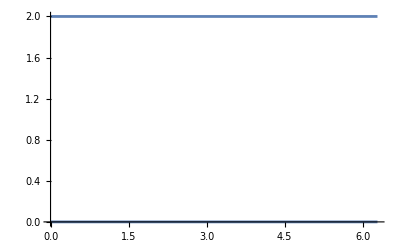

```mathematica
Plot[Eigenvalues[Cos[θ] PauliMatrix[1] - Sin[θ]  PauliMatrix[2] + IdentityMatrix[2]]  ,{θ,0,2Pi}]
```

```mathematica
Eigensystem[Cos[θ] PauliMatrix[1] - Sin[θ]  PauliMatrix[2]]
```

{{-1,1},{{-Cos[θ]-ⅈ Sin[θ],1},{Cos[θ]+ⅈ Sin[θ],1}}}